```mathematica
p1 = Plot3D[x1^2-x2^2- 15,{x1, -10, 10}, {x2, -10, 10}];
p2 = Plot3D[x1 x2+ 4,{x1, -10, 10}, {x2, -10, 10}, PlotStyle->Purple];
p3 = Plot3D[0,{x1, -10, 10}, {x2, -10, 10}, PlotStyle-> Red ];
Show[p1, p2,p3, ImageSize->Large]
```

-Graphics3D-

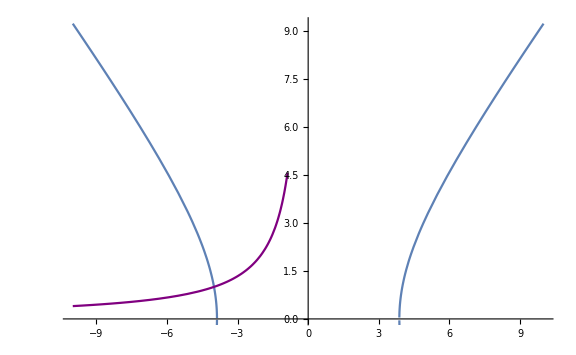

```mathematica
p4 = Plot[Sqrt[x1^2- 15],{x1, -10, 10}];
p5 = Plot[-Sqrt[x1^2- 15],{x1, -10, 10}];
p6 = Plot[-4/x1,{x1, -10, 10}, PlotStyle->Purple];
Show[p4, p5, p6, ImageSize->Large]
```

```mathematica
f[x_]=Expand[(x−0.1)(x−0.22)(x−0.55)(x−0.7)(x−0.75)]
```

-0.0063525+0.121495 x-0.75595 x^2+1.9845 x^3-2.32 x^4+x^5

```mathematica
f'[x]
```

0.121495-1.5119 x+5.9535 x^2-9.28 x^3+5 x^4